```mathematica
sumIntAng[n_]:=(n-2)*π;
```

```mathematica
regularAngle[n_]:=sumIntAng[n]/n;
```

```mathematica
sumCosRegAng[n_]:=n*Cos[regularAngle[n]];
```

```mathematica
sumSimple=FullSimplify[sumCosRegAng[n]]
```

-n Cos[(2 π)/n]

```mathematica
sumCos=N/@Table[{i,sumCosRegAng[i]},{i,3,12,1}];sumCos//Prepend[#,{"N","Σcos"}]&//Grid[#,Frame->All,Alignment->Left]&
```

N | Σcos
3. | 1.5
4. | 0.
5. | -1.54508
6. | -3.
7. | -4.36443
8. | -5.65685
9. | -6.8944
10. | -8.09017
11. | -9.25379
12. | -10.3923

```mathematica
ll=ListLinePlot[sumCos,Epilog->{PointSize@Large,Point@sumCos},PlotStyle->Red,
Frame->True,FrameStyle->Medium,FrameLabel->{"N","Σcos"},
PlotLabel->Style[TraditionalForm@sumSimple,16]];
```

```mathematica
pl=Plot[sumCosRegAng[x],{x,3,12},PlotStyle->Darker@Green];
```

```mathematica
graphSum[n_]:=6 - (3/2)n;
```

```mathematica
Show[{ll,pl,Plot[graphSum[x],{x,3,12},PlotStyle->Blue]},GridLines->Automatic,ImageSize->Large]
```

-Graphics-

```mathematica
Plot[graphSum[x],{x,3,7},Frame->True,GridLines->True]
```

-Graphics-

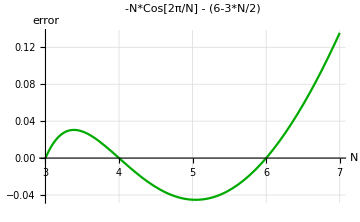

```mathematica
Plot[sumCosRegAng[x]-graphSum[x],{x,3,7},PlotStyle->Darker@Green,Axes->True,AxesStyle->Medium,AxesLabel->{"N","error"},GridLines->Automatic,ImageSize->Medium,PlotLabel->Style["-N*Cos[2π/N] - (6-3*N/2)",{Black,14}]]
```

```mathematica
N@Limit[(sumCosRegAng[x]-graphSum[x])/graphSum[x],x->4]
```

0.0471976

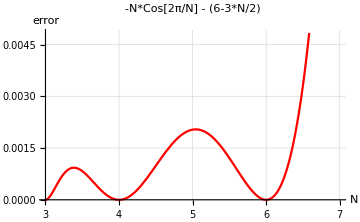

```mathematica
Plot[(sumCosRegAng[x]-graphSum[x])^2,{x,3,7},PlotStyle->Red,Axes->True,AxesStyle->Medium,AxesLabel->{"N","error"},GridLines->Automatic,ImageSize->Medium,PlotLabel->Style["-N*Cos[2π/N] - (6-3*N/2)",{Black,14}]]
```